```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
lT=20;
startT=1;
alist=Table[Flatten[Import["bdata/b"<>ToString[i]<>".dat"]],{i,1,lT}];
alist1=Table[Rest[alist[[i]]],{i,1,lT}];
V1=Flatten[Transpose[Table[Flatten[Import["./dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
ρmin=0.;
ρmax=10000.;
```

```mathematica
driv1=Table[Re[SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[alist[[i]]],100]/.{ρ->0}],{i,1,lT}];
```

```mathematica
T=Table[Exp[Log[10^-4]-(Log[10^-4]-Log[100])/20*(i-1)]//N,{i,1,lT}];
slop=Table[{SetPrecision[Log[T[[i]]/124.69765],90],SetPrecision[Re[FindFit[Transpose[{-Log[T/124.69765],Log[1/√V1]}][[i;;i+1]],a x+b,{a,b},x][[1]][[2]]],90]},{i,1,lT-1}];
```

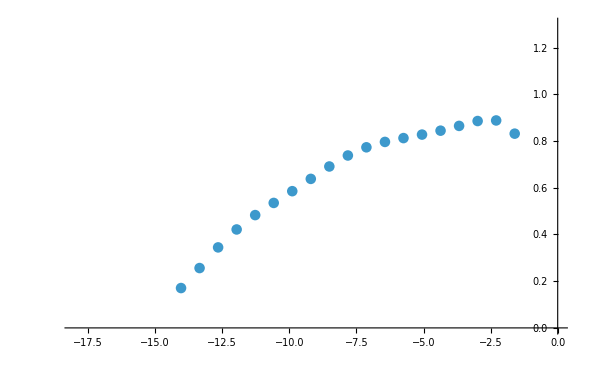

```mathematica
ListPlot[slop,ScalingFunctions->{Automatic,Automatic},PlotRange->{{-18,0},{0.,1.3}}]
```

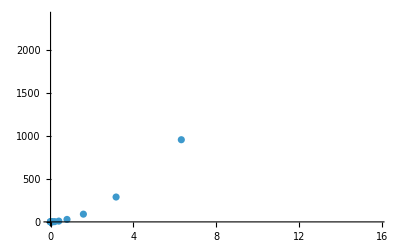

```mathematica
ListPlot[Transpose[{T,V1}],ScalingFunctions->{Automatic,Automatic}]
```

```mathematica
V1
```

{0.001288324079452408884268490852823994,0.0016308928829377304101365969163840814,0.0023238302692024943006623803552623201,0.0037416008637133100521275973383215921,0.0066987339211396190628146006398198981,0.013056954666162276251791785352519593,0.027348533315675532659538660657410139,0.061410086639088184828805322464739107,0.14829970095426471234606306462202469,0.38538195008964723004184632660526575,1.068751186280795487021521308465608,3.1109339958809230135361633094149601,9.3484233914533833729875786957486385,28.73661125868864974862240075921555,90.180898305299188275011718150873001,289.64714613008146825507850177838216,956.94171343848703157374737800874587,3253.9989101045811405506646978435139,11102.60997198497203881880820514591,35035.060378510558700590693134919466}